## RCP simulation figures

## Import Data

```mathematica
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social"];
```

```mathematica
rcp2p6Data=Import["export_data/rcp_sims/rcp2p6.dat","Data"];
rcp4p5Data=Import["export_data/rcp_sims/rcp4p5.dat","Data"];
rcp6Data=Import["export_data/rcp_sims/rcp6.dat","Data"];
rcp8p5Data=Import["export_data/rcp_sims/rcp8p5.dat","Data"];
```

```mathematica
TMBcolours=ColorData[97,"ColorList"];
```

```mathematica
(* Import figure from Knutti paper (Nature climate change *)
knuttiImg=Import["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/climate_social/figures/cmip5_projections.png",ImageSize->350,ImageResolution->100];
```

## Organise data

```mathematica
numSims=40;
tStep=0.1;
tmax=500;
tSeries=Range[1800,2300,tStep];
```

```mathematica
rcp2p6Data//Dimensions
```

{80,5001}

```mathematica
rcp2p6Temp=rcp2p6Data[[numSims+1;;]];
rcp4p5Temp=rcp4p5Data[[numSims+1;;]];
rcp6Temp=rcp6Data[[numSims+1;;]];
rcp8p5Temp=rcp8p5Data[[numSims+1;;]];
```

```mathematica
(*rcp2p6Traj=rcp2p6Data[[1,;;]];
rcp4p5Traj=rcp4p5Data[[1,;;]];
rcp6Traj=rcp6Data[[1,;;]];
rcp8p5Traj=rcp8p5Data[[1,;;]];
*)
```

### Find 95th quartiles

```mathematica
{lowerQuart,midQuart,upperQuart}={0.05,0.5,0.95};
```

```mathematica
tmax/tStep+1
```

5001.

```mathematica
rcp6Traj//Dimensions
```

{5001}

```mathematica
{lowerrcp2p6,medrcp2p6,upperrcp2p6}=Table[Quantile[rcp2p6Temp[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;
{lowerrcp4p5,medrcp4p5,upperrcp4p5}=Table[Quantile[rcp4p5Temp[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;
{lowerrcp6,medrcp6,upperrcp6}=Table[Quantile[rcp6Temp[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;
{lowerrcp8p5,medrcp8p5,upperrcp8p5}=Table[Quantile[rcp8p5Temp[[;;,i]],{lowerQuart,midQuart,upperQuart}],{i,1,tmax/tStep+1}]//Transpose;
```

### Image Options

```mathematica
(* time ticks *)
timeTicks=Table[{50(i-1),1800+50(i-1)},{i,1,13}];

(* imgs size *)
imgs=325;
(* aspect ratio *)
aratio=0.6;
(* legend position (scaled) *)
legendPos={0.2,0.7};
(* labels (alphabet) *)
labels=Alphabet[];
(* label position (scaled) *)
labelPos={0.05,0.91};
(* bold label on off *)
bold=1;
```

```mathematica
{padLeft,padRight,padBottom,padTop}={50,30,65,40};  (* image padding *)
```

```mathematica
(* time plot range *)
plRange={100,400};
(* social plot range *)
plRangeSoc={-0.02,1.05};
(* emissions plot range *)
plRangeEm={-0.5,18.5};
(* temperature plot range *)
plRangeTemp={-0.1,5.3};
```

```mathematica
(* colour of shading *)
Clear[shade]
shade[colour_]:=Directive[Opacity[0.5],Lighter[colour,0.6]]
```

```mathematica
{#,shade[#],shade[#]}&/@TMBcolours[[{1,7,2,4}]]//Flatten
```

{RGBColor[0.368417, 0.506779, 0.709798],Directive[Opacity[0.5],RGBColor[0.7473668, 0.8027116, 0.8839192]],Directive[Opacity[0.5],RGBColor[0.7473668, 0.8027116, 0.8839192]],RGBColor[0.363898, 0.618501, 0.782349],Directive[Opacity[0.5],RGBColor[0.7455592, 0.8474003999999999, 0.9129396]],Directive[Opacity[0.5],RGBColor[0.7455592, 0.8474003999999999, 0.9129396]],RGBColor[0.880722, 0.611041, 0.142051],Directive[Opacity[0.5],RGBColor[0.9522888, 0.8444164, 0.6568204]],Directive[Opacity[0.5],RGBColor[0.9522888, 0.8444164, 0.6568204]],RGBColor[0.922526, 0.385626, 0.209179],Directive[Opacity[0.5],RGBColor[0.9690103999999999, 0.7542504, 0.6836716]],Directive[Opacity[0.5],RGBColor[0.9690103999999999, 0.7542504, 0.6836716]]}

```mathematica
(* temperature ticks in accordance with CMIP5 comparison where baseline is temperature in 2000 *)
{tSeries[[2001]],rcp2p6Temp[[1,2001]]}
```

{2000.,1.05555}

```mathematica
(* shift temperature ticks so zerod in year 2000 *)
tempTicks={Range[-1,6]+1.056,Range[-1,6]}//Transpose
```

{{0.056,-1},{1.056,0},{2.056,1},{3.056,2},{4.056,3},{5.056,4},{6.056,5},{7.056,6}}

```mathematica
(* generic plot options *)
opts={PlotStyle->Flatten[{#,shade[#],shade[#]}&/@TMBcolours[[{1,7,2,4}]]],
Filling->{2->{{1},shade[TMBcolours[[1]]]},
3->{{1},shade[TMBcolours[[1]]]},
5->{{4},shade[TMBcolours[[7]]]},
6->{{4},shade[TMBcolours[[7]]]},
8->{{7},shade[TMBcolours[[2]]]},
9->{{7},shade[TMBcolours[[2]]]},
11->{{10},shade[TMBcolours[[4]]]},
12->{{10},shade[TMBcolours[[4]]]}},
FrameTicks->{{tempTicks,tempTicks},{Automatic,None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImageSize->350,
Frame->True,
LabelStyle->14,
ImagePadding->{{padLeft,padRight},{padBottom,padTop}}};
```

### Make plots

```mathematica
legend=LineLegend[TMBcolours[[{1,7,2,4}]],{"RCP2.6","RCP4.5","RCP6","RCP8.5"},LabelStyle->12]
```

```mathematica
Transpose[{tSeries,lowerrcp2p6}]//Dimensions
```

{5001,2}

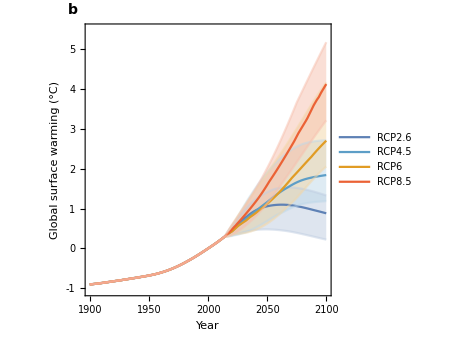

```mathematica
(* temperature trajecotires *)
rcpTempPlot=ListLinePlot[{Transpose[{tSeries,medrcp2p6}][[1000;;3000]],
Transpose[{tSeries,lowerrcp2p6}][[1000;;3000]],
Transpose[{tSeries,upperrcp2p6}][[1000;;3000]],
Transpose[{tSeries,medrcp4p5}][[1000;;3000]],
Transpose[{tSeries,lowerrcp4p5}][[1000;;3000]],
Transpose[{tSeries,upperrcp4p5}][[1000;;3000]],
Transpose[{tSeries,medrcp6}][[1000;;3000]],
Transpose[{tSeries,lowerrcp6}][[1000;;3000]],
Transpose[{tSeries,upperrcp6}][[1000;;3000]],
Transpose[{tSeries,medrcp8p5}][[1000;;3000]],
Transpose[{tSeries,lowerrcp8p5}][[1000;;3000]],
Transpose[{tSeries,upperrcp8p5}][[1000;;3000]]},
PlotRange->{{1900,2100},{0,5.5+1.056}},
opts,
PlotRangeClipping->False,
Epilog->Text[Style[labels[[2]],14,If[bold==1,Bold]],Scaled[{-0.05,1.05}]],
FrameLabel->{{"Global surface warming (°C)",None},{"Year","ESM, RCP scenarios"}},
PlotLegends->Placed[legend,Scaled[legendPos]],
AspectRatio->1]
```

## Image Grid

```mathematica
knuttiImgFormat=Show[knuttiImg,Epilog->Text[Style[labels[[1]],14,If[bold==1,Bold]],Scaled[{0.1,0.98}]],PlotRangeClipping->False,ImageResolution->100]
```

-Graphics-

```mathematica
rcpComparison=Grid[{{knuttiImgFormat,rcpTempPlot}}]
```

-Graphics-

```mathematica
Export["figures/fig_rcpComparison.png",rcpComparison,ImageResolution->300];
```